```mathematica
(* Seeing if can determine B^x along x-dir to one higher order than lowest order *)
(* Sasha would determine dBdx's polynomial coefficients for left and right cells centered on cell center, where point-valued dBx/dx is known from differencing a2c_i B^i across cell center *)
(* Here x/dx=0 is cell center, x/dx=1/2 is right cell face of interest and x/dx=-1/2 is the left cell face of interest *)
dBdxraw[x_]:=F0+F1/dx (x/dx-0) + F2 /dx(x/dx-0)^2+ F3 /dx(x/dx-0)^3+ F4 /dx(x/dx-0)^4;
```

```mathematica
(* The dBdxraw has constraints, but let place them later through the use of the a2c_i function *)
```

```mathematica
(* Now form integral that is distribution of Bx in the left and right cell with Bxl0 and Bxr0 cell center point values of field *)
Bx[t_]:=Bx0+Integrate[Evaluate[dBdxraw[x]],{x,0*dx,t}]
```

```mathematica
(* Now setup equation that determines Bx0, that is a2c_i B^i = known quantity *)
(* We want to form a2c_i B^i, which requires forming another function f=a2c_i Bx such that c2a_i f=Bx *)
f[x_]:=f0+f1/dx (x/dx-0) + f2 /dx(x/dx-0)^2+ f3 /dx(x/dx-0)^3+ f4 /dx(x/dx-0)^4+ f5 /dx(x/dx-0)^5;
RunningAverage[t_]:=FullSimplify[Integrate[f[x],{x,t-dx/2,t+dx/2}]/dx];
```

```mathematica
(* Now obtain coefficients of f from those of Bx *)
```

```mathematica
sol=Solve[CoefficientList[RunningAverage[x],x] ==CoefficientList[Bx[x],x],{f0,f1,f2,f3,f4,f5}]
```

{{f1→1/240 (240 dx^2 F0-20 dx F2+7 dx F4),f0→1/960 (960 Bx0-40 F1+7 F3),f2→1/8 (4 dx F1-dx F3),f3→1/6 (2 dx F2-dx F4),f4→(dx F3)/4,f5→(dx F4)/5}}

```mathematica
a2cBx[x_]:=f[x]//.sol[[1]]
```

```mathematica
(* now have a2c_i B^i distribution that has to give back known a2c_i B^i's, use this to obtain Bxl0 and Bxr0 assuming rest will correctly give back correct distribution of B^i *)
```

```mathematica
fun1=FullSimplify[a2cBx[1/2*dx]]
fun2=FullSimplify[a2cBx[-1/2*dx]]
sol=FullSimplify[Solve[{fun1==a2cright,fun2==a2cleft},{Bx0,F0}]]
FullSimplify[(fun1-fun2)/dx//.sol[[1]]]
```

Bx0+1/120 (60 dx F0+10 F1-F3)

Bx0+1/120 (-60 dx F0+10 F1-F3)

{{Bx0→1/120 (60 a2cleft+60 a2cright-10 F1+F3),F0→(-a2cleft+a2cright)/dx}}

(-a2cleft+a2cright)/dx

```mathematica
(* Get final Bxl and Bxr distributions *)
```

```mathematica
myBx[x_]:=FullSimplify[Bx[x]//.sol[[1]]]
```

0.65+0.3 x

0.12 (1.53619+x) (3.73423+(-1.32973+x) x) (0.765085+x (0.210207+x))

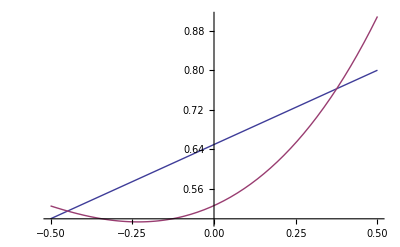

```mathematica
toplotBxlinear=FullSimplify[myBx[x]//.{dx->1,a2cleft->.5,a2cright->.8,F1->0,F2->0,F3->0,F4->0}]
toplotBxnonlinear=FullSimplify[myBx[x]//.{dx->1,a2cleft->.5,a2cright->.8,F1->1.5,F2->.9,F3->.2,F4->.6}]
Plot[{toplotBxlinear,toplotBxnonlinear},{x,-1/2,1/2}]
```

```mathematica
(* Get final a2c_i B^i distributions *)
mya2cBx=FullSimplify[a2cBx//.sol[[1]]]
```

(160 a2cleft dx^2 (dx^3-8 x^3)+160 a2cright dx^2 (dx^3+8 x^3)-(dx^2-4 x^2) (20 dx F3 x^2+16 F4 x^3+5 dx^3 (8 F1+F3-64 F0 x)))/(320 dx^5)

```mathematica
(* Check how a2cB^i is set *)
```

```mathematica
FullSimplify[mya2cBx//.{x->1/2*dx}]
FullSimplify[mya2cBx//.{x->-1/2*dx}]
```

a2cright

a2cleft

```mathematica
(* We DO get back a2cB at the face! good. *)
```

```mathematica
(* Assume don't care if face point values are different *)
```

```mathematica
(* Get point values at faces just to see *)
```

```mathematica
FullSimplify[myBx//.{t->1/2*dx}]
FullSimplify[myBx//.{t->-1/2*dx}]
```

a2cright

a2cleft

```mathematica
(* no change? *)
```